```mathematica
wave:= 1/Sqrt[11] Sum [SphericalHarmonicY[j,0,theta,phi]E^(I j Pi/4)E^(-I b j (j + 1)t /hbar),{j,0,10}]
```

```mathematica
b := 198.96 hbar 2 Pi 3 10^8
```

```mathematica
hbar:=1.055*10^(-34)
```

```mathematica
func := Evaluate[wave]
```

```mathematica
funcconj:=Evaluate[func*]
```

```mathematica
innerfuncrs:=Sum[func funcconj Cos[theta]^2 Sin[theta] 2Pi/100 Pi/100,{theta,0,Pi,Pi/100},{phi,0,2Pi,2Pi/100}]
```

```mathematica
innerfunc:=NIntegrate[Evaluate[func funcconj Cos[theta]^2 Sin[theta]] ,{theta,0,Pi},{phi,0,2Pi}]
```

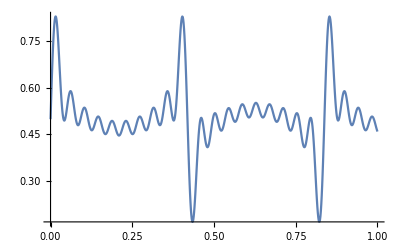

```mathematica
Plot[innerfunc,{t,0,10^-11},PlotRange->All]
```